https://mathematica.stackexchange.com/questions/95786/how-to-count-all-cliques-not-just-maximal-ones-in-graphs/97654

```mathematica
findAllCliques[g_]:=
DeleteDuplicates[Sort/@Flatten[Map[Subsets,FindClique[g,Infinity,All]],1]];
```

```mathematica
n=RandomInteger[25];
```

```mathematica
m=RandomInteger[Binomial[n,2]];
```

```mathematica
rgr=Graph[RandomGraph[{n,m}],VertexLabels->"Name"];
```

```mathematica
allCliques=findAllCliques[rgr];
```

```mathematica
Print["n = ",n,"m = ",m]
Print[Length@allCliques," Cliques found"]
```

n = 22m = 192

20954 Cliques found

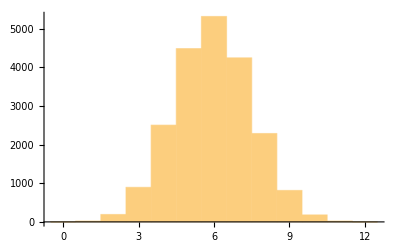

```mathematica
Histogram@Map[Length,allCliques]
```

```mathematica
VertexList[rgr]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

```mathematica
Intersection[allCliques,{{1,3}}]
```

{{1,3}}

```mathematica
allCliques
```

{{},{1},{3},{5},{7},{8},{11},{13},{14},{18},{20},{21},{22},{1,3},{1,5},{1,7},{1,8},{1,11},{1,13},{1,14},{1,18},{1,20},{1,21},{1,22},{3,5},{3,7},{3,8},{3,11},{3,13},{3,14},{3,18},{3,20},{3,21},{3,22},{5,7},{5,8},{5,11},{5,13},{5,14},{5,18},{5,20},{5,21},{5,22},{7,8},{7,11},{7,13},{7,14},{7,18},{7,20},{7,21},{7,22},{8,11},{8,13},{8,14},{8,18},{8,20},{8,21},{8,22},{11,13},20837,{2,14,17},{2,8,14,17},{2,14,17,20},{2,14,17,21},{2,14,17,22},{2,8,14,17,20},{2,8,14,17,21},{2,8,14,17,22},{2,14,17,20,21},{2,14,17,20,22},{2,14,17,21,22},{2,8,14,17,20,21},{2,8,14,17,20,22},{2,8,14,17,21,22},{2,14,17,20,21,22},{2,8,14,17,20,21,22},{2,14,17,19},{2,8,14,17,19},{2,14,17,19,21},{2,14,17,19,22},{2,8,14,17,19,21},{2,8,14,17,19,22},{2,14,17,19,21,22},{2,8,14,17,19,21,22},{2,14,16,17},{14,16,17,20},{2,8,14,16,17},{2,14,16,17,20},{2,14,16,17,21},{8,14,16,17,20},{14,16,17,20,21},{2,8,14,16,17,20},{2,8,14,16,17,21},{2,14,16,17,20,21},{8,14,16,17,20,21},{2,8,14,16,17,20,21},{2,14,16,17,19},{2,8,14,16,17,19},{2,14,16,17,19,21},{2,8,14,16,17,19,21},{3,14,16,17,20},{3,8,14,16,17,20},{3,14,16,17,20,21},{3,8,14,16,17,20,21},{12,15,16,20},{8,12,15,16,20},{12,15,16,18,20},{12,15,16,20,21},{8,12,15,16,18,20},{8,12,15,16,20,21},{12,15,16,18,20,21},{8,12,15,16,18,20,21},{2,9,14,17},{2,9,14,17,20},{2,9,14,17,21},{2,9,14,17,20,21},{2,9,14,17,19},{2,9,14,17,19,21}}
 |  |  |  |

```mathematica
allCliques2=findAllCliques[rgr];
```

```mathematica
allCliques2
```

```mathematica
FindClique[rgr,4,2]
```

{}

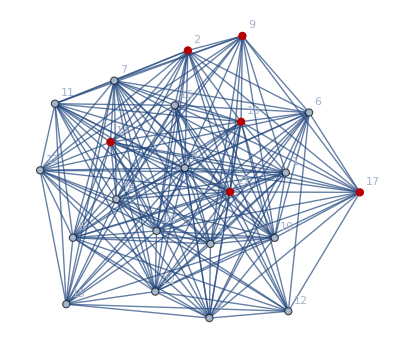

```mathematica
HighlightGraph[rgr,{2,9,14,17,19,21}]
```

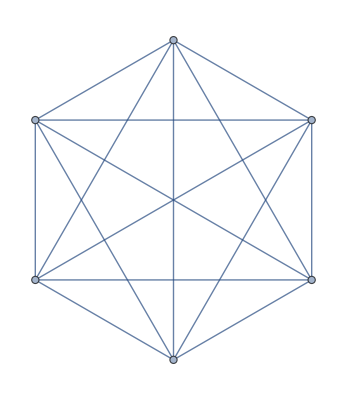

```mathematica
Subgraph[rgr,{2,9,14,17,19,21}]
```

```mathematica
FindClique[rgr,12,All]
```

```mathematica
Intersection[{{3,5,6,7},{9,67,4,5}}]
```

```mathematica
{{3,5,6,7},{9,67,4,5}}
```

```mathematica
Flatten[{{3,5,6,7},{9,67,4,5}}]
```

{3,5,6,7,9,67,4,5}

```mathematica
allitos=FindClique[rgr,Infinity,All];
```

```mathematica
allitos
```

{{1,3,5,7,8,11,13,14,18,20,21,22},{1,3,5,7,9,11,13,14,18,20,21},{1,3,4,6,7,8,10,18,19,21,22},{1,3,4,5,7,8,10,18,19,21,22},{1,3,4,5,7,8,14,18,19,21,22},{1,3,4,5,7,8,13,14,18,21,22},{1,3,5,7,8,10,11,18,20,21,22},{1,3,5,7,8,10,11,18,19,21,22},{1,3,5,7,8,11,14,18,19,21,22},{5,7,8,11,13,14,15,18,20,21,22},{2,5,7,8,11,13,14,18,20,21,22},{2,5,7,9,11,13,14,18,20,21},{1,3,5,7,9,10,11,18,20,21},{1,3,5,7,9,10,11,18,19,21},{1,3,5,7,9,11,14,18,19,21},{1,3,4,6,8,10,17,19,21,22},{3,4,6,7,8,10,16,18,19,21},{1,3,6,7,8,13,18,20,21,22},{1,3,6,7,8,10,18,20,21,22},{1,3,4,6,7,8,13,18,21,22},{4,5,7,8,10,15,18,19,21,22},{4,5,7,8,14,15,18,19,21,22},{4,5,7,8,13,14,15,18,21,22},{5,7,8,10,11,15,18,20,21,22},{2,5,7,8,10,11,18,20,21,22},{5,7,8,10,11,15,18,19,21,22},{2,5,7,8,10,11,18,19,21,22},{5,7,8,11,14,15,18,19,21,22},{2,5,7,8,11,14,18,19,21,22},{2,5,7,9,10,11,18,20,21},{2,5,7,9,10,11,18,19,21},{2,5,7,9,11,14,18,19,21},{1,3,6,7,9,13,18,20,21},{1,3,6,7,9,10,18,20,21},{1,3,6,7,9,10,18,19,21},{1,3,4,8,14,17,19,21,22},{3,4,6,8,10,16,17,19,21},{1,3,6,8,10,17,20,21,22},{4,5,8,12,15,18,19,21,22},{4,7,8,14,15,16,18,19,21},{3,4,7,8,14,16,18,19,21},{7,8,11,14,15,16,18,20,21},{3,7,8,11,14,16,18,20,21},{2,7,8,11,14,16,18,20,21},{7,8,11,14,15,16,18,19,21},{3,7,8,11,14,16,18,19,21},{2,7,8,11,14,16,18,19,21},{3,6,7,8,10,16,18,20,21},{2,6,7,8,10,16,18,20,21},{7,8,10,11,15,16,18,20,21},{3,7,8,10,11,16,18,20,21},{2,7,8,10,11,16,18,20,21},{7,8,10,11,15,16,18,19,21},{4,7,8,10,15,16,18,19,21},{2,7,8,10,11,16,18,19,21},{2,6,7,8,10,16,18,19,21},{3,7,8,10,11,16,18,19,21},{2,6,7,8,13,18,20,21,22},{2,6,7,8,10,18,20,21,22},{2,6,7,8,10,18,19,21,22},{2,6,7,9,13,18,20,21},{2,6,7,9,10,18,20,21},{2,6,7,9,10,18,19,21},{1,3,6,9,10,17,20,21},{1,3,6,9,10,17,19,21},{3,4,8,14,16,17,19,21},{1,3,8,14,17,20,21,22},{4,6,8,12,17,19,21,22},{4,6,8,12,16,17,19,21},{2,6,8,12,17,20,21,22},{2,6,8,12,17,19,21,22},{2,6,8,12,16,17,20,21},{2,6,8,12,16,17,19,21},{2,6,8,10,17,20,21,22},{2,6,8,10,17,19,21,22},{2,6,8,10,16,17,20,21},{2,6,8,10,16,17,19,21},{3,6,8,10,16,17,20,21},{5,8,12,15,18,20,21,22},{2,5,8,12,18,20,21,22},{2,6,8,12,18,20,21,22},{2,6,8,12,16,18,20,21},{2,5,8,12,18,19,21,22},{2,6,8,12,18,19,21,22},{2,6,8,12,16,18,19,21},{4,6,8,12,18,19,21,22},{4,6,8,12,16,18,19,21},{4,8,12,15,16,18,19,21},{2,6,9,10,17,20,21},{2,6,9,10,17,19,21},{1,3,9,14,17,20,21},{1,3,9,14,17,19,21},{2,8,14,17,20,21,22},{2,8,14,17,19,21,22},{2,8,14,16,17,20,21},{2,8,14,16,17,19,21},{3,8,14,16,17,20,21},{8,12,15,16,18,20,21},{2,9,14,17,20,21},{2,9,14,17,19,21}}

```mathematica
Subsets[{1,3,5,7,8,11,13,14,18,20,21,22}]
```

{{},{1},{3},{5},{7},{8},{11},{13},{14},{18},{20},{21},{22},{1,3},{1,5},{1,7},{1,8},{1,11},{1,13},{1,14},{1,18},{1,20},{1,21},{1,22},{3,5},{3,7},{3,8},{3,11},{3,13},{3,14},{3,18},{3,20},{3,21},{3,22},{5,7},{5,8},{5,11},{5,13},{5,14},4019,{1,3,7,8,11,14,18,20,21,22},{1,3,7,8,13,14,18,20,21,22},{1,3,7,11,13,14,18,20,21,22},{1,3,8,11,13,14,18,20,21,22},{1,5,7,8,11,13,14,18,20,21},{1,5,7,8,11,13,14,18,20,22},{1,5,7,8,11,13,14,18,21,22},{1,5,7,8,11,13,14,20,21,22},{1,5,7,8,11,13,18,20,21,22},{1,5,7,8,11,14,18,20,21,22},{1,5,7,8,13,14,18,20,21,22},{1,5,7,11,13,14,18,20,21,22},{1,5,8,11,13,14,18,20,21,22},{1,7,8,11,13,14,18,20,21,22},{3,5,7,8,11,13,14,18,20,21},{3,5,7,8,11,13,14,18,20,22},{3,5,7,8,11,13,14,18,21,22},{3,5,7,8,11,13,14,20,21,22},{3,5,7,8,11,13,18,20,21,22},{3,5,7,8,11,14,18,20,21,22},{3,5,7,8,13,14,18,20,21,22},{3,5,7,11,13,14,18,20,21,22},{3,5,8,11,13,14,18,20,21,22},{3,7,8,11,13,14,18,20,21,22},{5,7,8,11,13,14,18,20,21,22},{1,3,5,7,8,11,13,14,18,20,21},{1,3,5,7,8,11,13,14,18,20,22},{1,3,5,7,8,11,13,14,18,21,22},{1,3,5,7,8,11,13,14,20,21,22},{1,3,5,7,8,11,13,18,20,21,22},{1,3,5,7,8,11,14,18,20,21,22},{1,3,5,7,8,13,14,18,20,21,22},{1,3,5,7,11,13,14,18,20,21,22},{1,3,5,8,11,13,14,18,20,21,22},{1,3,7,8,11,13,14,18,20,21,22},{1,5,7,8,11,13,14,18,20,21,22},{3,5,7,8,11,13,14,18,20,21,22},{1,3,5,7,8,11,13,14,18,20,21,22}}
 |  |  |  |

```mathematica
ciclosdetres=FindCycle[rgr,3,All]
```

{{19<->21,21<->22,22<->19},{18<->22,22<->21,21<->18},{16<->19,19<->21,21<->16},{16<->21,21<->17,17<->16},{15<->22,22<->18,18<->15},{20<->18,18<->15,15<->20},{17<->21,21<->19,19<->17},{17<->16,16<->19,19<->17},878,{1<->11,11<->21,21<->1},{1<->13,13<->21,21<->1},{1<->14,14<->21,21<->1},{1<->17,17<->21,21<->1},{1<->19,19<->21,21<->1},{1<->18,18<->21,21<->1},{1<->20,20<->21,21<->1},{1<->22,22<->21,21<->1}}
 |  |  |  |

```mathematica
Intersection[ciclosdetres,{{19<->21,21<->22,22<->19}}]
```

{{19<->21,21<->22,22<->19}}

```mathematica
Intersection[ciclosdetres,{{21<->22,22<->19,19<->21}}]
```

{}

```mathematica
g=WheelGraph[4];
```

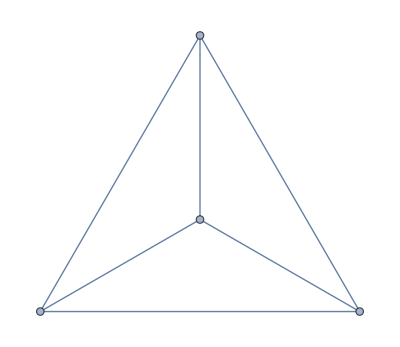

```mathematica
g
```

```mathematica
FindCycle[g]
```

{{1<->4,4<->3,3<->1}}

```mathematica
FindCycle[g,{Infinity},1]
```

{}

```mathematica
Table[FindCycle[g,{i},1],{i,1,4,1}]
```

```mathematica
{{},{},{{1<->4,4<->3,3<->1}},{{1<->4,4<->2,2<->3,3<->1}}}
```

```mathematica
Table[Length[Flatten[FindCycle[g,{i},1]]],{i,3,4,1}]
```

{3,4}

```mathematica
graphote=RandomGraph[{300,989}];
```

```mathematica
Table[Length[Flatten[FindCycle[graphote,{i},1]]],{i,3,Length[VertexList[graphote]],1}]
```

```mathematica
FindCycle[graphote,{265},1]
```

$Aborted

```mathematica
3==4
```

False

```mathematica
{4<->2}=={2<->8}
```

{4<->2}=={2<->8}

```mathematica
Intersection[{4,2},{4,2}]
```

{2,4}

```mathematica
tres=Length[Flatten[FindCycle[rgr,{3},All]]]
```

2682

```mathematica
cuatro=Length[Flatten[FindCycle[rgr,{4},All]]]
```

42168